# UP- AND DOWN- QUARK MASSES FROM QCD SUM RULES

```mathematica
(*Written in Mathematica 11.3*)
```

This notebook provides code to calculate the mass of the up- and down- quarks using finite energy sum rules. It is intended as a supplement to the paper: Dominguez , Mes, Schilcher, ‘Up- and Down- Quark Masses from QCD Sum Rules’, (2018) and to the dissertation: Mes ‘Light Quark Masses from QCD Sum Rules’, (2019).  

Always check for the latest version in the git repository: 
https://github.com/AlexesMes/light-quark-masses . 
(This repository also contains additional resources which would be of interest to the reader.) 

Please cite the journal paper if any part of this code is used in your own research.
This work is licensed under the Creative Commons Attribution-ShareAlike 4.0 International License. To view a copy of this license, visit http://creativecommons.org/licenses/by-sa/4.0/ or send a letter to Creative Commons, PO Box 1866, Mountain View, CA 94042, USA.

Mathematica code written by A. Mes
ORCID ID: 0000-0002-1187-7655
Corresponding email address: MSXALE002@myuct.ac.za
Last revised: 08-February-2019.

This determination  represents  a  substantial  improvement  on  the  previous FESR results for the up- and down- quark masses (Dominguez, Nasrallah, Rontsch, Schilcher, 'Up- and down- quark masses from finite-energy QCD sum rules to five loops' (2009)), in terms of the high numerical precision achieved in this calculation. The calculations have been computed in Mathematica, a modern 64 - bit computer language with natural support for precision real and complex numbers. At a minimum, using the machine precision corresponds to 16 digits of mantissa, although higher multiples of the machine precision can be used. In comparison, the previous 2009 determination was performed using Fortran 77 and Fortran 90, a 1977 and 1991 computer language respectively. Typically, the early standard Fortran versions only contain single precision (numbers accurate to 7 digits of mantissa), while double precision (typically 14 digits of mantissa) can be specified for real numbers. Complex numbers present more of an issue, as the double precision must be split between the real and imaginary components. Notwithstanding this, it is the confluence of these different working numerical precisions in earlier Fortran languages that can typically result in an accumulated error. The issue of numerical precision can make a notable impact on the results. For example, in CIPT where the renormalization group equations must be solved at 10 000 points around the circular contour, with each point relying on the previous value of the strong coupling as an initial condition, the opportunity for numerical carried error is pronounced. In Mathematica the numerical underflow in such a situation can be managed with greater care. The determination we present in this paper (laid out in the following Mathematica notebook), therefore represents a significant advancement in achieved numerical precision of FESR determinations of the up - and down - quark masses.

```mathematica
<<GeneralUtilities` 
<<ErrorBarPlots`
```

```mathematica
SetSystemOptions["CheckMachineUnderflow"->False]; (*This supresses undeflow warning messages*)
```

### Initialize Constants - Global Inputs

```mathematica
(*Threshold energy. Source: Bijnens, Prades, deRafael, 'Light Quark Masses in QCD' (1995).*)
sth=9*mpi^2;
(*Pion Pole data (mπ and fπ)[in MeV]. Source: (Particle Data Group), Phys.Rev.D 98,030001 (2018),'Leptonic decays of charged pseudoscalar mesons'.*)
mpi = 134.9770/1000;fpi = 92.07/1000;
(*sint0 = (mτ)^2 = initial reference energy, aint0 = (coupling strength at s = sint0)/ π. uncert0 = (uncertainty in coupling strength at s = sint0)/ π. 
Source: M.Tanabashi et al.(Particle Data Group), Phys.Rev.D 98,030001 (2018).*)
sint0= (1.77686)^2; aint0=0.3205/Pi;uncert0 = 0.0183/Pi;
(*Three light quark flavours: up, down and strange*)
nf=3; 
(*Gluon condensate, <α/π G^2>.
 Source: Dominguez, Hernandez, Schilcher, 'Determination of the gluon condensate from data in the charm-quark region' (2015).*)
GluonCon= 0.037; uncertGluonCon=0.015; 
(*Ratio mu/md=0.48 (+0.07- 0.08), used to seperate the up- and down-quark mass. Source: M.Tanabashi et al.(Particle Data Group), Phys.Rev.D 98,030001 (2018).*)
ratiomumd=0.48;ratiomu=(0.48/(1+0.48)); ratiomd=(1/(1+0.48)) ;
uncertratio=0.075; (*where the asymetric error has been averaged*)
```

Note: The Particle Data Group gives the world average of the strong coupling to be: α_s(m_Z^2)=0.1181+ 0.0011 . (Source: M.Tanabashi et al.(Particle Data Group), Phys.Rev.D 98,030001 (2018)).
We have then used version 3 of RunDec (a Mathematica package for running and decoupling of the strong coupling and quark masses)  to run the coupling to the m_τ scale, decoupling over flavour thresholds. We find α_s(m_τ^2)=0.3205 + 0.0183 . (Source: K. Chetyrkin, J. Kühn and M. Steinhauser, arXiv preprint hep-ph/0004189 (2000)).

# Hadronic Spectrum

In the hadronic sector, the spectral function of the current correlator ψ_5(q^2), involves the pion pole followed by the three-pion resonance contribution. This section elaborates on the method to model the hadronic resonances using a sum of Breit-Wigner forms.

### Choosing a Kernel

There is a freedom in the choice of kernel P_5(s). The most effective kernel is: P_5(s) = (s-a)(s-s_0). This is the integration kernel which quenches the hadronic spectrum at s_0 (the radius of the circular contour in the complex energy plane) and between the two resonance peaks. Source: Bodenstein et. al, ‘Strange quark mass from sum rules with improved QCD convergence’ (2013). 
Note: Comparison of quark masses using a different kernels is given in the last section of this notebook.

```mathematica
(*The coefficent in the  kernel which causes it to vanish between the two pionic excitations. aC is exactly half-way betweent the two pionic exctations: aC = (1.56)^2*)
aC =2.4; 
(*The chosen kernel*)
kern1[s_,s0_] := (s-aC)*(s-s0);
```

### Breit - Wigner Modelling

Modelling the Hadronic Resonances with a sum of Breit-Wigner Forms. Here, the threshold behaviour of the three-pion
state is modelled beyond the chiral limit. Hence, the threshold is at s_th=9 m_π^2.  Source: Bijnens, Prades, de Rafael, ‘Light Quark Masses in QCD’ (1995).  Using the approximate threshold behaviour in the chiral limit instead, has a limited impact on the final quark mass. This is explored in the Comparison Section towards the end of this notebook.

```mathematica
modelBPdR[s_,λc_,width1_,width2_,κ_]:=Module[{Γpi1 ,Γpi2 ,λ,m,Γ,BW,BW1,BW2,P},
mpi1= 1300/1000   ;Γpi1 = width1/1000;mpi2 = 1812/1000;Γpi2 = width2/1000;λ=κ*λc;
(*Breit-Wigner model normalized such that: BW1(0)=BW2(0)=1 *)
BW= (((m^2-sth)^2+ m^2*Γ^2)/((s-m^2)^2+ m^2*Γ^2)); 
BW1 = BW/. {m-> mpi1,Γ-> Γpi1};BW2= BW/. {m-> mpi2,Γ-> Γpi2};
IPS[k_?NumericQ]:=NIntegrate[Sqrt[1-(4*mpi^2)/u]*Sqrt[(1-(Sqrt[u]+mpi)^2/k)*(1-(Sqrt[u]-mpi)^2/k)]*(5+1/2*1/((k-mpi^2)^2)*((k-3u+3*mpi^2)^2+3*(k-(Sqrt[u]+mpi)^2)*(k-(Sqrt[u]-mpi)^2)*(1-(4*mpi^2)/u)+20*mpi^4)+1/(k-mpi^2)*(3*(u-mpi^2)-k+9*mpi^2)),{u,4*mpi^2,(Sqrt[k]-mpi)^2},WorkingPrecision->12];
 P= 1/(9*2^8*π^4) * mpi^4/fpi^2*IPS[s]*(BW1 +λ*BW2)/(1+λ)*HeavisideTheta[s-9*mpi^2];
Return[P]];
```

Note : The free parameter λ controls the relative importance of the second radial excitation. Chose λ such that it results in a reasonably smaller weight of the second resonance compared to the first. If you wish to estimate  the error in the constant λ (that determines the weighting of the resonances), we would adjust the factor λ_c. λ_c=1 is the default value.

# QCD Section

## RGE for α and m_s

Renormalization Group Equations to determine the running coupling constant α_s(s),  and the running mass m_q(s) at a chosen scale. 
For example, we would find a_s(s0) by using: apwrexpand[s0,aint,sint]. In Contour Improved Perturbation Theory, a_s(s0) is the initial condition in solving the RGE for the coupling constant at each point around the circle with radius s_0 in the complex energy plane.

### QCD β-Coefficients

```mathematica
(*The known β co-efficients of QCD. Source: Baikov, Chetyrkin, Kühn, 'Five-Loop Running of the QCD coupling constant'(2017). Reference to earlier co-efficient determinations is given in this paper.*)

b0C=1/4(11-2/3 nf);
b1C=1/16(102-38/3 nf);
b2C=1/64 (2857/2 -5033/18 nf +325/54 nf^2);
b3C=1/256 (149753/6 +3564Zeta[3]-(1078361/162+6508/27 Zeta[3]) nf+(50065/162+6472/81 Zeta[3])nf^2+1093/729 nf^3);
b4C=1/4^5 (8157455/16+621885/2*Zeta[3]-88209/2*Zeta[4]-288090*Zeta[5]+nf*(-336460813/1944-4811164/81*Zeta[3]+33935/6*Zeta[4]+1358995/27*Zeta[5])+
           nf^2*(25960913/1944+698531/81*Zeta[3]-10526/9*Zeta[4]-381760/81*Zeta[5])+
nf^3*(-630559/5832-48722/243*Zeta[3]+1618/27*Zeta[4]+460/9*Zeta[5])+
nf^4*(1205/2916-152/81*Zeta[3]));
```

### QCD γ-Coefficients

```mathematica
(*The known γ co-efficients of QCD. Source: Baikov, Chetyrkin, Kühn, 'Quark Mass and Field Anomalous Dimensions to order Subscript[α, s]^5' (2014). Reference to earlier co-efficient determinations is given in this paper.*)
```

```mathematica
g0C =1;
g1C = 1/16(202/3-20/9*nf);

g2C = 1/64(1249-(2216/27+ 160/3*Zeta[3])*nf )-140/81*nf^2;

g3C = 1/256(4603055/162+135680/27*Zeta[3]-8800*Zeta[5]+(-91723/27-34192/9*Zeta[3]+880*Zeta[4] + 18400/9*Zeta[5])*nf 
    +( 5242/243+800/9*Zeta[3]-160/3*Zeta[4])*nf^2 +(-332/243+64/27*Zeta[3])*nf^3);
g4C = 1/4^5(99512327/162+46402466/243*Zeta[3]+96800*Zeta[3]^2-698126/9*Zeta[4]-231757160/243*Zeta[5]+242000*Zeta[6]+412720*Zeta[7]
   +nf*(-150736283/1458-12538016/81*Zeta[3]-75680/9*Zeta[3]^2+2038742/27*Zeta[4]+49876180/243*Zeta[5]-638000/9*Zeta[6]-1820000/27*Zeta[7])
   +nf^2*(1320742/729+2010824/243*Zeta[3]+46400/27*Zeta[3]^2-166300/27*Zeta[4]-264040/81*Zeta[5]+92000/27*Zeta[6])
   +nf^3*(91865/1458+12848/81*Zeta[3]+448/9*Zeta[4]-5120/27*Zeta[5])+nf^4*(-260/243-320/243*Zeta[3]+64/27*Zeta[4]));
```

### RGE for the running coupling constant, α_s

```mathematica
(*Using the renormalization group equation for Subscript[a, s](s) = (Subscript[α, s](s))/π one can perform a
Taylor expansion at some given reference scale s = sint, leading to the equation below. This equation can be used to determine the running coupling constant at any chosen scale. Source: Davier, Hocker, Zhang, 'The physics of hadronic tau decays'(2005).*)

apwrexpand[s_,aint_,sint_]:=
aint +aint^2*(-b0C*Log[s/sint]) +aint^3*(-b1C*Log[s/sint] + b0C^2*(Log[s/sint])^2)+aint^4*(-b2C*Log[s/sint] +5/2 *b0C*b1C*(Log[s/sint])^2-b0C^3*(Log[s/sint])^3)  +aint^5*(-b3C*Log[s/sint] +3/2 *b1C^2*(Log[s/sint])^2+3*b0C*b2C*(Log[s/sint])^2 -13/3*b0C^2*b1C*Log[s/sint]^3+ b0C^4*(Log[s/sint])^4)+aint^6*(-b4C*Log[s/sint]+7/2*b0C*b1C*(Log[s/sint])^2+7/2*b0C*b3C*(Log[s/sint])^2-35/6*b0C*b1C^2*(Log[s/sint])^3-6*b0C^2*b2C*(Log[s/sint])^3+77/12*b0C^3*b1C*(Log[s/sint])^4-b0C^5*(Log[s/sint])^5);
```

### RGE for the running mass, m_q

```mathematica
(*The renormalization group equation for the running mass Subscript[m, q](s), can be integrated directly in order to find Subscript[m, q](s) at any chosen scale. Source: A. Mes, J. Stephens, 'An Application of Rubi: Series Expansion of the Quark Mass Renormalization Group Equation' arXiv:1811.04892(2018).*)

mqRGE[s_,mqs0_,aint_,sint_,s0_]:=mqs0*Exp[Integrate[(g0C+a*g1C+a^2*g2C+a^3*g3C+a^4*g4C)/(a*b0C+a^2*b1C+a^3*b2C+a^4*b3C+a^5*b4C),{a,apwrexpand[s0,aint,sint],apwrexpand[s,aint,sint]}]];

(*Note: As for Subscript[a, s](s), a similar taylor expansion of the running mass RGE exists. It can be used in place of the above equation. To order Subscript[α, s]^4 it is given in: Chetyrkin, Kniehl,Sirlin, 'Estimations of order α^3 and α^4 corrections to mass-dependent obesrvables'(1997); to order Subscript[α, s]^5 it is given by: Mes, Stephens arXiv:1811.04892(2018).*)
```

## Theoretical Input: Correlators and Kernels

## pQCD

The pseudoscalar correlator (phi5) is given in this section. 
For Contour Improved Perturbation Theory, we need a correlator where the quadratic divergence is not present in order to perform the renormalization group improvement (eliminating the logarithmic terms in the correlator by setting μ^2=-s). Hence, in CIPT we actually consider the second derivative of the pseudoscalar correlator. The second derivative of the pseudoscalar correlator, with the RG improvement performed is denoted by: d2phi5.

### Wilson Coefficients

```mathematica
(*The Wilson Co-efficients entering the OPE for Subscript[n, f]=3. Source: Dominguez, Nasrallah, Rontsch, Schilcher, 'Up- and down- quark masses from finite-energy QCD sum rules to five loops' (2009).*)
C01 = 6;
C11 = 34;
C12 = -6;
C21 =N[ -105*Zeta[3] + 9631/24];
C22 = -95;
C31 =N[4748953/864- π^4/6 -91519/36 *Zeta[3]+ 715/2*Zeta[5]];
C32 =N[ -6(4781/18 -475/8*Zeta[3])];
C41 = 33532.263638321;
C42 = -15230.646220931589;

K0 = C01;
K1=C11+2*C12;
K2=C21+2*C22;
K3=C31+2*C32;
K4=C41+2*C42;
```

### pQCD Correlator

```mathematica
phi5[A_]:= -ms0^2*s/(16*Pi^2)*(6*Log[-s/muo^2] -12 
	+a*(-6*Log[-s/muo^2]^2+34*Log[-s/muo^2] -36.651)
	+a^2*(8.5*Log[-s/muo^2]^3-95*Log[-s/muo^2]^2+275.08*Log[-s/muo^2]-304.79)
	+a^3*(-13.813*Log[-s/muo^2]^4+229*Log[-s/muo^2]^3 -1165.4*Log[-s/muo^2]^2+2795.1*Log[-s/muo^2]-2966.2)
	+A*a^4*(24.172*Log[-s/muo^2]^5-534.05*Log[-s/muo^2]^4+3962.5*Log[-s/muo^2]^3 -15231*Log[-s/muo^2]^2+33532*Log[-s/muo^2]));
phi5A[A_]:= phi5[A]/ms0^2;
(*The perturbative QCD function has been evaluated at Subscript[n, f]=3. Note: ms0 = (Subscript[m, u]+Subscript[m, d])^2, muo^2 denotes μ^2, and Subscript[a, s]=Subscript[α, s]/π (ie. a=alpha/Pi).*)
```

```mathematica
(*Second Derivative of correlator - used in CIPT*)
```

```mathematica
d2phi5[A_]:= -ms0^2*1/(16*Pi^2)*1/s*(K0+K1*a+K2*a^2+K3*a^3+A*K4*a^4);
```

Note: A is a factor which allows us to estimate the uncertainty in the mass due to the unknown a^5 term in the PQCD correlator. Default value: A=1.  When calculating 
this uncertainty we assume the a^5 term to be equal to the a^4 term(by setting A=2), and calculate the change in the mass.

## Condensates

### Non - perturbative Contributions to the OPE

```mathematica
(*The gluon condensate contribution to the OPE. Used in Fixed Order Perturbation Theory. Note: ms0 = (Subscript[m, u]+Subscript[m, d])^2, and GG = <α/π G^2>. Source: Chetrykin, Dominguez, Pirjol,Schilcher 'Mass singularities in light quark correlators:The strange quark case' (1995).*)
phiG[GG_]:=-ms0^2/(8*s)*GG*(1+a*(11/2-2*Log[-s/muo^2]));
phiG1[GG_]:= phiG[GG]/ms0^2;
```

```mathematica
(*Second derivative of the gluon condensate contribution to the OPE. Used in Contour Improved Perturbation Theory. The renormalization group improvement (which removes the logaritmic terms) has already been performed.*)
d2phiG[GG_]:=-ms0^2/s^3*1/4*GG*(1+ 11/2*a);
```

## CIPT Functions

The coupling strength, α_S(s), is a function of the energy in the complex energy plane, s, to be integrated. The RG improvement is performed before the integration, this eliminates all the logarithmic terms. The strong coupling, α_s, and the running masses, m_ud, are numerically integrated around the circle. At each point around the circle (i.e. at each value of φ), α_s(s) must be obtained by solving the Renormalization Group Equation (RGE). The same must be done for the running quark mass, m_ud.
The function contourimproved[kernelcontribution_,correlator_, step_,aint_,sint_,s0_] , implements the Contour Improved Perturbation Theory Method, and outputs the contour integral ∮_(|s|=s_0) ds (correlator*kernel)  using a Riemann Sum to perform the integration.

```mathematica
contourimproved[kernelcontribution_,correlator_, step_,aint_,sint_,s0_] := Module[{h,rgealpha, ralpha, rgemass, rmass, contourintegral},
h=Pi/step;
(*Solving Subscript[α, s](s) renormalization group differential equation, between -π and π. The output is the running coupling constant given 
as an interpolation function over the points q, where q ranges linearly between -π and π.*)
rgealpha=NDSolve[{ar'[q]==-I(b0C ar[q]^2+b1C ar[q]^3+b2C ar[q]^4) ,ar[0]==apwrexpand[s0,aint,sint]},ar,{q,-Pi,Pi}]; 
(*The value of the strong coupling is then tabulated at discrete points around the circle in the complex s-plane.*)
ralpha=Table[Evaluate[ar[x]/.rgealpha],{x,h,Pi,h}];
(*Calculating the running mass at each point around the circle, by using the value of the coupling 
constant and solving the Subscript[m, q](s) renormalization group differential equation at each discrete point. Note: The list of Subscript[α, s] at each point between-π and π is given by ralpha.*)
rgemass=Accumulate[Table[h*(g0C *ralpha[[k]] +g1C *ralpha[[k]]^2+g2C *ralpha[[k]]^3+g3C *ralpha[[k]]^4),{k,1,step}]];
rmass=Exp[-I*rgemass];
(*In order to perform the contour integral, the following change of variables is made: s=-s0*Exp[I*x] and ds=-s0*I*Exp[I*x]*dx*)
contourintegral=Total[Table[h*(2*Re[(-1/(2*Pi*I))*(-s0*I*Exp[I*k*h])*(correlator/.muo-> Sqrt[s0]/. s -> (-s0*Exp[I*k*h]) /. ms0 -> rmass[[k]]/. a ->ralpha[[k]])*(kernelcontribution/.s ->(-s0*Exp[I*k*h]))])
               ,{k,1,step}]];
Return[contourintegral]]
```

Note: 
1).  We integrate  the result, by taking the limit of a large number of points around the circle and summing over all these points - i.e. a Riemann Sum.
2). Doubling the integral between ϵ  (where ϵ  > 0)  and π,should be equivalent to performing the integral between 0 and 2*π, but it avoids the branch cut along the real axis.
3). We take the real part of the contour integral, because we require δPQCD to be real, although (α_s(-s))/π is complex.  

A very important fact to note is that when calculating the coupling constant  and running mass at each discrete point around the circle, do not start at x=0 (i.e. on the real axis),  since in our circular contour in the complex energy plane there is a branch cut along the real axis. Rather start at x = ϵ = h. When one has 10 000 points (for example), h= π/10 000  - this means one approximately starts at x=0.

## FOPT Functions

The strong coupling, α_s(s), and the quark mass, m_ud, are frozen around the circle in the complex energy plane. The RG improvement is performed after the integration, to eliminate all the logarithmic terms. 
The function fixedorder[correlator_, aint_,sint_,s0_,as_] , implements the Fixed Order Perturbation Theory Method, and outputs the contour integral ∮_(|s|=s_0) ds (correlator*kernel)  using a fixed coupling α0 at a chosen energy scale s0.

```mathematica
fixedorder[correlator_,aint_,sint_,s0_,as_]:=Module[{contourintegral,contint},
(*In order to perform the contour integral, the following change of variables is made: s=-s0*Exp[I*x] and ds=-s0*I*Exp[I*x]*dx*)
(*Renormalization Group Improvement is performed by setting muo^2=s0, this removes the logarithmic terms*)
contourintegral=Integrate[(-s0* I *Exp[I*x])*(correlator/.muo-> Sqrt[s0]/.a-> as/.s->( -s0* Exp[I*x])),{x,-Pi,Pi}];
Return[contourintegral]
];
```

# Calculating the Quark Mass: FESR approach

## Finite Energy Sum Rule - Mass Function

Using quark - hadron duality to equate the QCD and Hadronic contributions. This isolates m_ud,the mass of the up- and down- quarks (in GeV) at a scale of s0 (in GeV^2). From this we use the recent PDG result mu/md=0.48 (ratiomd, ratiomu), to separate the mass of the up quark at a scale of s0 and the mass of the down quark at a scale of s0. Then the function mqRGE[s_,mqs0_,aint_,sint_,s0_] is used to run the quark mass to any required scale. 
FOPT and CIPT need to be treated slightly differently, hence two mass functions: CIPTmassFESR[] and FOPTmassFESR[].

### Contour Improved Mass Function

```mathematica
CIPTmassFESR[s0_,aint_,sint_,model_,kernel_,GG_,A_,correlator_]:=Module[{res,pole,hadronic,Steps,kernelcont,deltaPQCD,deltaGluon,deltaQCD,muds0,mds0,mus0,mudats,mdats,muats },

(*For the Hadronic contribution to the FESR due to the hadronic resonances, we integrate the hadronic spectral function from the threshold energy sth, up to the radius of our circle in the complex energy plane s0.*)
res= NIntegrate [model*kernel[s,s0],{s,sth,s0}];
(*Hadronic Contribution due to the pion pole.*)
pole = 2*fpi^2 * mpi^4*kernel[mpi^2,s0];
hadronic =res+pole ;

(*Integrating the chosen kernel twice, in order to multiply it by our physical/double-derived correlators (d2phiG, d2phi5). See note below.*)
kernelcont= Module[{G,Gs,Gs0,Fs,Fs0,F,d2kern},
G[z_]:=Integrate[kernel[v,s0],{v,0,z}];
Gs=G[s];
Gs0=Gs/.s->s0;
F[z_]:= Integrate[G[k],{k,0,z}]-Gs0*z;
Fs=F[s];
Fs0=Fs/.s->s0;
d2kern=Fs-Fs0
];

(*Number of points around the circular contour.*)
Steps =10000;
(*PQCD contribution to the OPE*)
deltaPQCD=Extract[contourimproved[kernelcont,correlator[A],Steps,aint,sint,s0],{1,1}];
(*Non-perturbative Contributions to the OPE: corrections to the FESR from the gluon condensate.*)
deltaGluon=Extract[contourimproved[kernelcont,d2phiG[GG],Steps,aint,sint,s0],{1,1}];
(*The total Quantum Chromodynamic contribution to the FESR: includes perturbative contributions and non-perturbative contributions*)
deltaQCD =deltaPQCD+deltaGluon;

(*Mass at a scale s0. Multiplication by 1000 to convert from GeV to MeV*)
muds0= (hadronic/deltaQCD)^(1/2)*1000/2 ; (*muds0=(mass of up quark + mass of down quark)/2*)
mds0=2* muds0*ratiomd ;(*mds0= mass of down quark*)
mus0 =2*muds0*ratiomu;(*mus0= mass of up quark*)

(*Rescaling the mass: Using the RGE for the running mass to find mudats (i.e. mud(s)), mdats (i.e. md(s)) and muats (i.e. mu(s)) at a specified scale, here s =(2 GeV)^2.*)
mudats=mqRGE[4,muds0,aint,sint,s0];
mdats=mqRGE[4,mds0,aint,sint,s0];
muats=mqRGE[4,mus0,aint,sint,s0];
Return[{mudats,mdats,muats}]
];
```

Note: in order to calculate the kernel contribution which we multiply by the second derivative of the correlator in the FESR, we make use of the mathematical theorems:
 ∮Δ(s)Φ(s) ds = -∮[G(s)-G(s0)](dΦ(s))/ds ds, with G(s)=∫_0^sΔ(s’) ds’ , and
  ∮Δ(s)Φ(s) ds = ∮[F(s)-F(s0)](d^2 Φ(s))/ds^2 ds, with F(s)=∫_0^s[G(s’)-G(s0)] ds’ =∫_0^s  [∫_0^s' Δ(s’’) ds’’ - ∫_0^s0  Δ(s’’) ds’’] ds’
  
Note: As expected, the quark mass output converges as the step size (Steps) get larger and larger. For example, between steps= 10 000 and steps= 100 000 the final quark mass only differs slightly in the third decimal place. To keep calculation speed resonably, we use a step size of 10 000.

### Fixed Order Mass Function

```mathematica
(*Expand framework allows for one to expand the square root and check the convergence of the δPQCD series. Default value: expand = 1. By setting expand = -1/2, the series will be taylor expanded. It is interesting to see how this affect the final quark mass: in terms of covergence, etc.*)
expand=1;
```

```mathematica
FOPTmassFESR[s0_,aint_,sint_,model_,kernel_,GG_,A_,correlator_]:=Module[{res,pole,hadronic,Steps,deltaPQCD,deltaPQCD0,deltaPQCD1,deltaPQCD2,deltaPQCD3,deltaPQCD4,deltaGluon,deltaQCD,deltaQCDI,as,muds0,mds0,mus0,mudats,mdats,muats},

(*Calculate the value of the coupling constant - this value is frozen around the circle.*)
as=apwrexpand[s0,aint,sint];

(*For the Hadronic contribution to the FESR due to the hadronic resonances, we integrate the hadronic spectral function from the threshold energy sth, to the radius of our circle in the complex energy plane s0.*)
res= NIntegrate [model*kernel[s,s0],{s,sth,s0}];
(*Hadronic Contribution due to the pion pole.*)
pole = 2*fpi^2 * mpi^4*kernel[mpi^2,s0];
hadronic =res+pole ;

(*Non-perturbative Contributions to the OPE: corrections to the FESR from the gluon condensate*)
deltaGluon=Re[fixedorder[phiG1[GG]*kernel[s,s0]*(-1/(2*Pi*I)),aint,sint,s0,as]];

(*PQCD contribution to the OPE*)
deltaPQCD0=Re[fixedorder[Coefficient[correlator[A],a,0]*kernel[s,s0]*(-1/(2*Pi*I)),aint,sint,s0,a]];
deltaPQCD1=Re[fixedorder[Coefficient[correlator[A],a,1]*kernel[s,s0]*(-1/(2*Pi*I)),aint,sint,s0,a]];
deltaPQCD2=Re[fixedorder[Coefficient[correlator[A],a,2]*kernel[s,s0]*(-1/(2*Pi*I)),aint,sint,s0,a]];
deltaPQCD3=Re[fixedorder[Coefficient[correlator[A],a,3]*kernel[s,s0]*(-1/(2*Pi*I)),aint,sint,s0,a]];
deltaPQCD4=Re[fixedorder[Coefficient[correlator[A],a,4]*kernel[s,s0]*(-1/(2*Pi*I)),aint,sint,s0,a]];

(*Assembling a series expansion in terms of the coupling constant*)
deltaPQCD=deltaPQCD0+deltaPQCD1*a+deltaPQCD2*a^2+deltaPQCD3*a^3+deltaPQCD4*a^4;

(*The total Quantum Chromodynamic contribution to the FESR: includes perturbative contributions and non-perturbative contributions*)
deltaQCD=deltaPQCD+deltaGluon;

(*Expand framework allows for one to expand the square root. Normal comand truncates the series after the a^4 term such that it becomes an expression*)
deltaQCDI=(Series[(deltaQCD)^expand,{a,0,4}]//Normal)/.a-> as;

(*Mass at a scale s = s0. Multiplication by 1000 to convert from GeV to MeV*)
muds0= (hadronic)^(1/2)(deltaQCDI)^(-1/(2*expand))*1000/2 ;(*muds0=(mass of up quark + mass of down quark)/2*)
mds0=2* muds0*ratiomd ;(*mds0= mass of down quark*)
mus0 =2*muds0*ratiomu;(*mus0= mass of up quark*)

(*Rescaling the mass: Using the RGE for the running mass to find mudats (i.e. mud(s)), mdats (i.e. md(s)) and muats (i.e. mu(s)) at a specified scale, here s=(2 GeV)^2.*)
mudats=mqRGE[4,muds0,aint,sint,s0];
mdats=mqRGE[4,mds0,aint,sint,s0];
muats=mqRGE[4,mus0,aint,sint,s0];
Return[{mudats,mdats,muats}]
];
```

## Uncertainty in the mass

Calculating the uncertainty in the quark mass, m_ud: the total uncertainty is due to the uncertainty in the coupling constant, the uncertainty in the gluon condensate, the uncertainty due to the range of s0, uncertainty in the hadronic model and the uncertainty in only knowing up to α_s^4 in the PQCD expression. The uncertainties are added in quadrature.

```mathematica
MassErrorFESR[s0_,modD_,kernel_,MassFESR_,correlator_]:=Module[{quarkmass,Δas,Δs00,Δs0,ΔHAD,ΔGG,Δtot,Δ6LOOP, massanderrors},
(*mass at 2GeV with standard input *)
quarkmass=MassFESR[s0,aint0,sint0,modD,kernel,GluonCon,1,correlator][[1]];

(*uncertainty in the coupling constant*)
Δas=MassFESR[s0,aint0+uncert0,sint0,modD,kernel,GluonCon,1,correlator][[1]]-quarkmass;

(*uncertainty in the gluon condensate*)
ΔGG=MassFESR[s0,aint0,sint0,modD,kernel,GluonCon+uncertGluonCon,1,correlator][[1]]-quarkmass;

(*uncertainty due to the range of s0 - vary Subscript[s, 0] by ±0.5 GeV^2 in the window of stability*)
Δs00=Table[MassFESR[i,aint0,sint0,modD,kernel,GluonCon,1,correlator][[1]],{i,s0-0.5,s0+0.5,0.1}];
Δs0=Abs[1/2*(Max[Δs00]-Min[Δs00])];

(*uncertainty in the hadronic model obtained by varying the hadronic parameters: width of first resonance (260 +- 36 MeV), width of second resonance (208 +- 12 MeV) and the parameter λ (0.1-0.2) within the acceptable ranges*)
ΔHAD=MassFESR[s0,aint0,sint0,modelBPdR[s,1,224,196,0.2],kernel,GluonCon,1,correlator][[1]]-MassFESR[s0,aint0,sint0,modelBPdR[s,1,296,220,0.1],kernel,GluonCon,1,correlator][[1]];

(*uncertainty in knowing the 6th loop of the PQCD term*)
Δ6LOOP=MassFESR[s0,aint0,sint0,modD,kernel,GluonCon,2,correlator][[1]]-quarkmass;

(*the total uncertainty addeed in quadrature*)
Δtot=Sqrt[Δas^2+ΔHAD^2+Δs0^2+ΔGG^2+Δ6LOOP^2];

massanderrors={{quarkmass,"Mass MeV"},{Δas,"Δα"},{ΔGG,"ΔGG"},{Δs0,"Δs0"},{Min[Δs00],Max[Δs00],"Min s0 and Max s0"},{ΔHAD,"Model Error"},{Δ6LOOP,"Unknown 6-loop PQCD term"},{Δtot,"Total"}};
Return[massanderrors]
];
```

Calculating the uncertainty in the up- and down- individual quark masses. The uncertainties in m_u and m_d are due to the uncertainty in m_ud (determined by the FESR) and the uncertainty in the ratio m_u/m_d(given by the PDG). Calculated using standard error propagation formula. Note : The input variable j can take on the values : j = 2,3. If j = 2, (FOPT/CIPT)massFESR[] outputs the uncertainty in m_d(s), if j = 3, (FOPT/CIPT)massFESR[] outputs m_u(s).

```mathematica
MassErrorFESRIndv[s0_,modD_,kernel_,MassFESR_,correlator_,j_]:=Module[{quarkmass,Δtot ,mud,Δmud,md,Δmd,mu,Δmu, massanderrors},
quarkmass=MassFESR[s0,aint0,sint0,modD,kernel,GluonCon,1,correlator];

(*Light quark mass (Subscript[m, ud]) and uncertainty at 2GeV with standard input *)
mud=quarkmass[[1]];
Δmud=MassErrorFESR[s0,modD,kernel,MassFESR,correlator][[8]][[1]];

(*The value of the down- or up- quark mass (j=2, or j=3 respectively)*)
md=quarkmass[[2]];
mu=quarkmass[[3]];

(*Uncertainty in Subscript[m, u] or Subscript[m, d]*)
(*Subscript[m, d] = (2*(Subscript[Subscript[m, u], d] +- Subscript[Δm, ud]))/(1+(Subscript[m, u]/Subscript[m, d] +- Δ Subscript[m, u]/Subscript[m, d]))*)
Δmd=(2*mud)/(1+ratiomumd)* Sqrt[((2*Δmud)/(2*mud))^2+(uncertratio/(1+ratiomumd))^2];
(*Note: when calculating Subscript[m, u] or Subscript[m, d], the factor of 2 is present due to the definition Subscript[m, ud]=(Subscript[m, u]+Subscript[m, d])/2. When multiplying the quark masses by a constant we mutliply the absolute uncertainty by the same constant*)
(*Subscript[m, u] = (Subscript[m, u]/Subscript[m, d] +- Δ Subscript[m, u]/Subscript[m, d])*(Subscript[m, d] +- Subscript[Δm, d])*)
Δmu=md*ratiomumd*Sqrt[(Δmd/md)^2+(uncertratio/ratiomumd)^2];

If[j==2,Δtot=Δmd;quarkmass=md,Δtot = Δmu;quarkmass=mu];

massanderrors={{quarkmass,"Mass MeV"},{Δtot,"Total"}};
Return[massanderrors]
];
```

# Results

## Graphing the Hadronic Spectral Function

Graphing the two pionic resonances modelled as a sum of Breit-Wigner forms.

```mathematica
hadronicgraph=Plot[{modelBPdR[x,1,260,208,0.1]*Pi},{x,mpi^2+0.1,4.4},PlotRange->{{0,4.5},{0,0.000045}}, Frame-> True,FrameStyle->Thick,FrameLabel-> {"s (GeV^2)","Im ψ_5(s)"},PlotStyle->{Directive[Thickness[0.004],Black]} ]
```

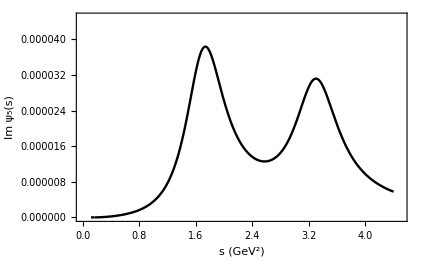
```mathematica
(*-Graphics-;*)
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"HadronicSpectrumGraph.pdf"}],hadronicgraph];
```

## Graphing the quark mass range of stability

Graph depicting how the quark mass, m_ud, (calculated using two different kernels) fluctuates over a range 1.5 < s0 < 4.0 . Note: s0 is the radius of our circle in the complex energy plane.

### Contour Improved Perturbation Theory

```mathematica
ciptstabilitydata=Table[{i,CIPTmassFESR[i,aint0,sint0,modelBPdR[s,1,260,208,0.1],kern1,GluonCon,1,d2phi5][[1]]},{i,1,4.0,0.1}]
ciptplot=ListLinePlot[{ciptstabilitydata},Frame-> True,FrameStyle->Thick,FrameLabel-> {"s_0 (GeV^2)","m_ud(2 GeV) (MeV)"},PlotStyle-> {Directive[Thickness[0.004],Black], Directive[Thickness[0.004],Black]},PlotRange-> {{1.45,4.05},{3,6}},PlotLabel->"Contour Improved Perturbation Theory"];
```

{{1., 4.89857}, {1.1, 4.76006}, {1.2, 4.63818}, {1.3, 4.53109}, {1.4, 4.43765}, {1.5, 4.35722}, {1.6, 4.28934}, {1.7, 4.23321}, {1.8, 4.1872}, {1.9, 4.14898}, {2., 4.11637}, {2.1, 4.08782}, {2.2, 4.06245}, {2.3, 4.03979}, {2.4, 4.01965}, {2.5, 4.00197}, {2.6, 3.98674}, {2.7, 3.97399}, {2.8, 3.96373}, {2.9, 3.95594}, {3., 3.95051}, {3.1, 3.94725}, {3.2, 3.94588}, {3.3, 3.94612}, {3.4, 3.94789}, {3.5, 3.95154}, {3.6, 3.95768}, {3.7, 3.9671}, {3.8, 3.98061}, {3.9, 3.99901}, {4., 4.02315}}

```mathematica
(*Calculating the error bar to plot on ciptplot1*)
mud2error2=MassErrorFESR[3.3,modelBPdR[s,1,260,208,0.1],kern1,CIPTmassFESR,d2phi5];
```

```mathematica
(*Plotting error bars*)
cipterrorbars=ErrorListPlot[{{{3.3,mud2error2[[1]][[1]]},ErrorBar[mud2error2[[8]][[1]]]}},PlotStyle-> {Black,Directive[Thickness[0.002]]}];
ciptplot1=Show[ciptplot,cipterrorbars]
```

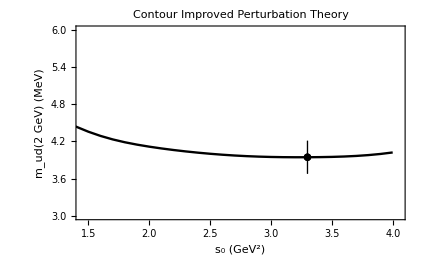
```mathematica
(*-Graphics-;*)
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"CIPTGraph.pdf"}],ciptplot1];
```

### Fixed Order Perturbation Theory

```mathematica
foptstabilitydata=Table[{i,FOPTmassFESR[i,aint0,sint0,modelBPdR[s,1,260,208,0.1],kern1,GluonCon,1,phi5A][[1]]},{i,1,4.0,0.1}]
foptplot=ListLinePlot[{foptstabilitydata},Frame-> True,FrameStyle->Thick,FrameLabel-> {"s_0 (GeV^2)","m_ud(2 GeV) (MeV)"},PlotStyle-> {Directive[Thickness[0.004],Black], Directive[Thickness[0.004],Black]},PlotRange-> {{1.45,4.05},{3,6}}, PlotLabel->"Fixed Order Perturbation Theory"];
```

{{1., 4.19359}, {1.1, 4.17163}, {1.2, 4.14335}, {1.3, 4.11243}, {1.4, 4.08172}, {1.5, 4.05353}, {1.6, 4.02961}, {1.7, 4.01094}, {1.8, 3.99724}, {1.9, 3.9873}, {2., 3.97977}, {2.1, 3.97374}, {2.2, 3.9688}, {2.3, 3.9649}, {2.4, 3.96214}, {2.5, 3.96072}, {2.6, 3.96087}, {2.7, 3.96282}, {2.8, 3.96677}, {2.9, 3.97284}, {3., 3.98111}, {3.1, 3.99153}, {3.2, 4.00395}, {3.3, 4.01825}, {3.4, 4.03452}, {3.5, 4.05325}, {3.6, 4.07528}, {3.7, 4.10165}, {3.8, 4.13347}, {3.9, 4.17192}, {4., 4.21828}}

```mathematica
(*Calculating the error bars to plot on foptplot*)
mud2error5=MassErrorFESR[3.3,modelBPdR[s,1,260,208,0.1],kern1,FOPTmassFESR,phi5A];
```

```mathematica
(*Plotting error bars*)
fopterrorbars=ErrorListPlot[{{{3.3,mud2error5[[1]][[1]]},ErrorBar[mud2error5[[8]][[1]]]}},PlotStyle-> {Black,Directive[Thickness[0.002]]}];

foptplot1=Show[foptplot,fopterrorbars]
```

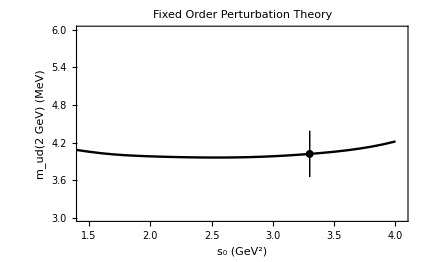
```mathematica
(*-Graphics-;*)
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"FOPTGraph.pdf"}],foptplot1];
```

The Fixed Order Results do not appear in the paper:  Dominguez , Mes, Schilcher, ‘Up- and Down- Quark Masses from QCD Sum Rules’ (2018), since their stability is slightly worse than the stability of the Contour Improved Results.  Further, FOPT results in a larger uncertainty in the quark masses than CIPT, mainly caused by the importance FOPT places on the unknown higher order terms in the δPQCD series.

## Calculating the up and down quark mass with uncertainties

Calculating m_ud(s), m_d(s), m_u(s) with uncertainties, at a scale s= (2 (GeV))^2. Set s_0  to be any value in the region of stability (between 1.8 GeV^2 and 4 GeV^2 for CIPT): for the paper we choose, s0 = 3.3 GeV^2.

```mathematica
Clear[s0];
s0=3.3;
```

### Contour Improved Perturbation Theory

```mathematica
mudCIPT=CIPTmassFESR[s0,aint0,sint0,modelBPdR[s,1,260,208,0.1],kern1,GluonCon,1,d2phi5][[1]]
mudErrorCIPT =MassErrorFESR[s0,modelBPdR[s,1,260,208,0.1],kern1,CIPTmassFESR,d2phi5]

mdCIPT=CIPTmassFESR[s0,aint0,sint0,modelBPdR[s,1,260,208,0.1],kern1,GluonCon,1,d2phi5][[2]]
mdErrorCIPT =MassErrorFESRIndv[s0,modelBPdR[s,1,260,208,0.1],kern1,CIPTmassFESR,d2phi5,2]

muCIPT=CIPTmassFESR[s0,aint0,sint0,modelBPdR[s,1,260,208,0.1],kern1,GluonCon,1,d2phi5][[3]]
muErrorCIPT =MassErrorFESRIndv[s0,modelBPdR[s,1,260,208,0.1],kern1,CIPTmassFESR,d2phi5,3]
```

3.94612
{{3.94612, "Mass MeV"}, {-0.206591, "Δα"}, {-0.052108, "ΔGG"}, {0.0173631, "Δs0"}, {3.94588, 3.98061, "Min s0 and Max s0"}, {0.084549, "Model Error"}, {-0.131837, "Unknown 6-loop PQCD term"}, {0.265002, "Total"}}
5.33259
{{5.33259, "Mass MeV"}, {0.44863, "Total"}}
2.55964
{{2.55964, "Mass MeV"}, {0.454233, "Total"}}

### Fixed Order Perturbation Theory

```mathematica
mudFOPT=FOPTmassFESR[s0,aint0,sint0,modelBPdR[s,1,260,208,0.1],kern1,GluonCon,1,phi5A][[1]]
mudErrorFOPT =MassErrorFESR[s0,modelBPdR[s,1,260,208,0.1],kern1,FOPTmassFESR,phi5A]

mdFOPT=FOPTmassFESR[s0,aint0,sint0,modelBPdR[s,1,260,208,0.1],kern1,GluonCon,1,phi5A][[2]]
mdErrorFOPT=MassErrorFESRIndv[s0,modelBPdR[s,1,260,208,0.1],kern1,FOPTmassFESR,phi5A,2]

muFOPT=FOPTmassFESR[s0,aint0,sint0,modelBPdR[s,1,260,208,0.1],kern1,GluonCon,1,phi5A][[3]]
muErrorFOPT=MassErrorFESRIndv[s0,modelBPdR[s,1,260,208,0.1],kern1,FOPTmassFESR,phi5A,3]
```

4.01825
{{4.01825, "Mass MeV"}, {-0.199707, "Δα"}, {-0.069275, "ΔGG"}, {0.083354, "Δs0"}, {3.96677, 4.13347, "Min s0 and Max s0"}, {0.0860946, "Model Error"}, {-0.278207, "Unknown 6-loop PQCD term"}, {0.36938, "Total"}}
5.43007
{{5.43007, "Mass MeV"}, {0.569984, "Total"}}
2.60643
{{2.60643, "Mass MeV"}, {0.490622, "Total"}}

# Convergence

The δPQCD series is only known up to the α_s^4 term and does not appear to converge. In this section we examine how this affects the quark masses calculated using Fixed Order Perturbation Theory and Contour Improved Perturbation Theory.

## Contour Improved Perturbation Theory: Graphing Convergence

```mathematica
Clear[s0];
s0=3.3;
```

```mathematica
(*The second derivative of the perturbative terms of pseudoscalar correlator (d2phi5) is given below. It is written out explicitly to order:α^0/π,α/π, α^2/π, α^3/π, α^4/π respectively*)
d2phi51[A_]:= {-ms0^2*1/(16*Pi^2)*1/s*(A*K0)};
d2phi52[A_]:= -ms0^2*1/(16*Pi^2)*1/s*(K0+A*K1*a);
d2phi53[A_]:= -ms0^2*1/(16*Pi^2)*1/s*(K0+K1*a+A*K2*a^2);
d2phi54[A_]:= -ms0^2*1/(16*Pi^2)*1/s*(K0+K1*a+K2*a^2+A*K3*a^3);
d2phi55[A_]:= -ms0^2*1/(16*Pi^2)*1/s*(K0+K1*a+K2*a^2+K3*a^3+A*K4*a^4);
```

```mathematica
(*Calculating the quark mass Subscript[m, ud], to each order of the perturbative correlator*)
(*Considering δPQCD up to term α^0/π*)
mudconverge0=MassErrorFESR[s0,modelBPdR[s,1,260,208,0.1],kern1,CIPTmassFESR,d2phi51];
(*Considering δPQCD up to term α/π*)
mudconverge1=MassErrorFESR[s0,modelBPdR[s,1,260,208,0.1],kern1,CIPTmassFESR,d2phi52];
(*Considering δPQCD up to term α^2/π*)
mudconverge2=MassErrorFESR[s0,modelBPdR[s,1,260,208,0.1],kern1,CIPTmassFESR,d2phi53];
(*Considering δPQCD up to term α^3/π*)
mudconverge3=MassErrorFESR[s0,modelBPdR[s,1,260,208,0.1],kern1,CIPTmassFESR,d2phi54];
(*Considering δPQCD up to term α^4/π*)
mudconverge4=MassErrorFESR[s0,modelBPdR[s,1,260,208,0.1],kern1,CIPTmassFESR,d2phi55];
```

```mathematica
(*Graphing the quark mass to each order*)
convCIPTplot=ErrorListPlot[{{{1,mudconverge0[[1]][[1]]},ErrorBar[mudconverge0[[8]][[1]]]},{{2,mudconverge1[[1]][[1]]},ErrorBar[mudconverge1[[8]][[1]]]},{{3,mudconverge2[[1]][[1]]},ErrorBar[mudconverge2[[8]][[1]]]},{{4,mudconverge3[[1]][[1]]},ErrorBar[mudconverge3[[8]][[1]]]},{{5,mudconverge4[[1]][[1]]},ErrorBar[mudconverge4[[8]][[1]]]}},AxesOrigin->{0,0}, Frame-> True,FrameLabel-> {None,"m_ud(2 GeV) (MeV)"},FrameStyle->Thick,FrameTicks->{{Automatic,None},{{{1,"O(α^0)"},{2,"O(α^1)"},{3,"O(α^2)"},{4,"O(α^3)"},{5," O(α^4)"}},None}},PlotStyle-> {Directive[Thickness[0.002],Black]},PlotRange-> {{0.8,5.2},{2.5,10.5}},PlotLegends->Placed[PointLegend[{"CIPT"}],{0.82,0.85}]]

Export[FileNameJoin[{NotebookDirectory[],"CIPTConvergeGraph.pdf"}],convCIPTplot];
```

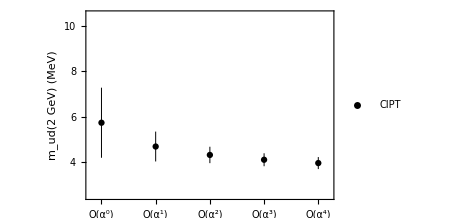
```mathematica
(*-Graphics-;*)
```

## Fixed Order Perturbation Theory: Graphing Convergence

```mathematica
(*The perturbative terms of pseudoscalar correlator (phi5) is given below. It is written out explicitly to order:α^0/π,α/π, α^2/π, α^3/π respectively.(Note: the correlator to order α^4/π appears earlier in the notebook.)*)
phi51[A_]= -ms0^2*s/(16*Pi^2)*A*(6*Log[-s/muo^2] -12 ); 
phi51A[A_]= phi51[A]/ms0^2;

phi52[A_]= -ms0^2*s/(16*Pi^2)*(6*Log[-s/muo^2] -12 
	+A*a*(-6*Log[-s/muo^2]^2+34*Log[-s/muo^2] -36.651)); 
phi52A[A_]= phi52[A]/ms0^2;

phi53[A_]= -ms0^2*s/(16*Pi^2)*(6*Log[-s/muo^2] -12 
	+a*(-6*Log[-s/muo^2]^2+34*Log[-s/muo^2] -36.651)
	+A*a^2*(8.5*Log[-s/muo^2]^3-95*Log[-s/muo^2]^2+275.08*Log[-s/muo^2]-304.79)); 
phi53A[A_]= phi53[A]/ms0^2;

phi54[A_]= -ms0^2*s/(16*Pi^2)*(6*Log[-s/muo^2] -12 
	+a*(-6*Log[-s/muo^2]^2+34*Log[-s/muo^2] -36.651)
	+a^2*(8.5*Log[-s/muo^2]^3-95*Log[-s/muo^2]^2+275.08*Log[-s/muo^2]-304.79)
	+A*a^3*(-13.813*Log[-s/muo^2]^4+229*Log[-s/muo^2]^3 -1165.4*Log[-s/muo^2]^2+2795.1*Log[-s/muo^2]-2966.2));
phi54A[A_]= phi54[A]/ms0^2;


(*Calculating the quark mass Subscript[m, ud], to each order of the perturbative correlator*)
(*Considering δPQCD up to term α^0/π*)
mudconvergeFOPT0=MassErrorFESR[s0,modelBPdR[s,1,260,208,0.1],kern1,FOPTmassFESR,phi51A];
(*Considering δPQCD up to term α/π*)
mudconvergeFOPT1=MassErrorFESR[s0,modelBPdR[s,1,260,208,0.1],kern1,FOPTmassFESR,phi52A];
(*Considering δPQCD up to term α^2/π*)
mudconvergeFOPT2=MassErrorFESR[s0,modelBPdR[s,1,260,208,0.1],kern1,FOPTmassFESR,phi53A];
(*Considering δPQCD up to term α^3/π*)
mudconvergeFOPT3=MassErrorFESR[s0,modelBPdR[s,1,260,208,0.1],kern1,FOPTmassFESR,phi54A];
(*Considering δPQCD up to term α^4/π*)
mudconvergeFOPT4=MassErrorFESR[s0,modelBPdR[s,1,260,208,0.1],kern1,FOPTmassFESR,phi5A];
```

```mathematica
(*Graphing the quark mass to each order*)
convFOPTplot=ErrorListPlot[{{{1,mudconvergeFOPT0[[1]][[1]]},ErrorBar[mudconvergeFOPT0[[8]][[1]]]},{{2,mudconvergeFOPT1[[1]][[1]]},ErrorBar[mudconvergeFOPT1[[8]][[1]]]},{{3,mudconvergeFOPT2[[1]][[1]]},ErrorBar[mudconvergeFOPT2[[8]][[1]]]},{{4,mudconvergeFOPT3[[1]][[1]]},ErrorBar[mudconvergeFOPT3[[8]][[1]]]},{{5,mudconvergeFOPT4[[1]][[1]]},ErrorBar[mudconvergeFOPT4[[8]][[1]]]}},AxesOrigin->{0,0}, Frame-> True,FrameLabel-> {None,"m_ud(2 GeV) (MeV)"},FrameStyle->Thick,FrameTicks->{{Automatic,None},{{{1,"O(α^0)"},{2,"O(α^1)"},{3,"O(α^2)"},{4,"O(α^3)"},{5," O(α^4)"}},None}},PlotStyle-> {Directive[Thickness[0.002],Gray]},PlotRange-> {{0.8,5.2},{2.5,10.5}},PlotLegends->Placed[SwatchLegend[{"FOPT"},LegendMarkers->{"▲",11}],{0.83,0.73}],PlotMarkers->{"▲",11},Joined->True]/.Line[pts:{{x1_?NumericQ,_},{x2_,_},{_,_}...}]/;x1≠x2->Nothing

Export[FileNameJoin[{NotebookDirectory[],"FOPTConvergeGraph.pdf"}],convFOPTplot];
```

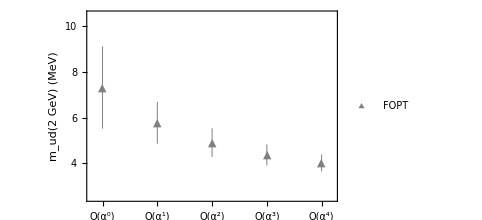
```mathematica
(*-Graphics-;*)
```

Comparing FOPT vs CIPT convergence

```mathematica
compareconvergence=Show[convCIPTplot,convFOPTplot]
Export[FileNameJoin[{NotebookDirectory[],"ConvergeGraph.pdf"}],compareconvergence];
```

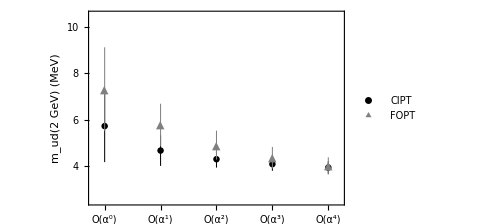
```mathematica
(*-Graphics-;*)
```

From the above graph one can see that the quark mass converges quicker when using the CIPT method. Therefore, CIPT places less importance on the unknown higher order terms in the δPQCD series, thereby reducing this uncertainty. 
The quark masses are calculated with a lower overall uncertainty in CIPT.

# Comparisons

This section explores how the light quark mass changes if one uses: a different kernel, the full hadronic spectral function beyond the chiral limit, or if one Taylor expands √δPQCD in order to examine the convergence of the series. Since Contour Improved Perturbation Theory is our method of choice, we only use CIPT to examine the effects on m_ud(s) these changes will have.

## Using different kernels

Various different kernels can be used in order to quench the hadronic resonances. Here we explore the effect of several different integration kernels on the stability of the quark mass. The first kernel (a), quenches the hadronic resonances at the two resonance peaks: P_5(s) = 1-a_0 s-a_1 s^2. This is the standard kernel which has been used before in determining the up- and down- quark masses. Source: Dominguez, Nasrallah, Rontsch, Schilcher, ‘Up- and down- quark masses from finite-energy QCD sum rules to five loops’ (2009). The second kernel (b), quenches the hadronic resonances at the two pionic resonance masses and at s_0: P_5(s) = (s-m_π1^2)(s-m_π2^2)(s_0-s). This is a pinched kernel which has been previously suggested to counteract potential duality violations . Source: Bodenstein, Dominguez, Schilcher, ‘Strange quark mass from sum rules with improved perturbative QCD convergence’ (2013). The third kernel (c), is the optimal kernel: P_5(s) = (s-a)(s-s_0) , which is explored in detail, earlier in this notebook.

```mathematica
(*Subscript[P, 5](s)= 1-Subscript[a, 0] s-Subscript[a, 1] s^2*)
a0C= 0.896;a1C = -0.1802 ;
kern2[s_,s0_] := 1- a0C*s-a1C*s^2;
ciptdifkerneldata=Table[{i,CIPTmassFESR[i,aint0,sint0,modelBPdR[s,1,260,208,0.1],kern2,GluonCon,1,d2phi5][[1]]},{i,1,4.0,0.1}];
ciptplot2=ListLinePlot[{ciptdifkerneldata},Frame-> True,FrameStyle->Thick,FrameLabel-> {"s_0 (GeV^2)","m_ud(2 GeV) (MeV)"},PlotStyle-> {Directive[Thickness[0.004],Black], Directive[Thickness[0.004],Black]},PlotRange-> {{1.45,4.05},{3,6}}]
```

```mathematica
(*Subscript[P, 5](s)= (s-Subscript[m, π1]^2)(s-Subscript[m, π2]^2)(Subscript[s, 0]-s)*)
kern3[s_,s0_]:= (s-mpi1^2)*(s-mpi2^2)*(s0-s);
ciptdifkerneldata3=Table[{i,CIPTmassFESR[i,aint0,sint0,modelBPdR[s,1,260,208,0.1],kern3,GluonCon,1,d2phi5][[1]]},{i,1,4.0,0.1}];
ciptplot3=ListLinePlot[{ciptdifkerneldata3},Frame-> True,FrameStyle->Thick,FrameLabel-> {"s_0 (GeV^2)","m_ud(2 GeV) (MeV)"},PlotStyle-> {Directive[Thickness[0.004],Black], Directive[Thickness[0.004],Black]},PlotRange-> {{1.45,4.05},{3,6}}]
```

```mathematica
comparekernels=Show[ciptplot,ciptplot2,ciptplot3,Epilog->{Text["(a)",{3.25,4.7}],Text["(b)",{3.25,4.34}],Text["(c)",{3.25,3.84}]}]
Export[FileNameJoin[{NotebookDirectory[],"KernelGraph.pdf"}],comparekernels];
```

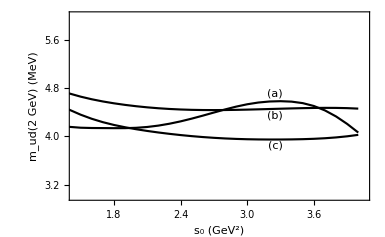
```mathematica
(*-Graphics-;*)
```

In the above graph: (a) P_5(s) = 1-a_0 s-a_1 s^2, (b) P_5(s) = (s-m_π1^2)(s-m_π2^2)(s_0-s) and (c) P_5(s) = (s-a)(s-s_0) .

From the above graph, we prefer kernel  (b) P_5(s) = (s-m_π1^2)(s-m_π2^2)(s_0-s) and (c) P_5(s) = (s-a)(s-s_0) due to stability considerations. However, several other criteria are taken into account when deciding on the optimal kernel.  For instance, the kernel should not bring in higher dimensional condensates,  as their values are poorly known. This constrains substantially the powers of s. Hence, we are lead to disfavour kernel (b) since it results in the dimension d = 8 condensate entering the FESR (whose value is completely unknown), which would bring in an unknown systematic uncertainty into the calculation. Hence, our preferred kernel is kernel (c)P_5(s) = (s-a)(s-s_0), which quenches the hadronic resonance contribution at s=s_0,  as well as in the region between the two resonances.

## Modelling the hadronic spectral function in the chiral limit

We can also model the hadronic spectral function in the chiral limit. In this case the threshold is at s_th=0. Source: Bijnens, Prades, de Rafael, ‘Light Quark Masses in QCD’ (1995).

```mathematica
Clear[sth];
sth=0; (*Threshold behaviour in chiral limit. Source: Davier, Hocker, Zhang, 'Physics of Hadronic Tau-decays'.*)
modelBPdR2[s_,λc_,width1_,width2_,κ_]:=Module[{mpi1,Γpi1 ,mpi2,Γpi2 ,λ,m,Γ,BW,BW1,BW2,P},
(*Mass and widths of the two pionic exications [in MeV]*)
mpi1= 1300/1000   ;Γpi1 = width1/1000;mpi2 = 1812/1000;Γpi2 = width2/1000;λ=κ*λc;
(*Breit-Wigner model normalized such that: BW1(0)= BW2(0)=1 *)
BW= (((m^2-sth)^2+ m^2*Γ^2)/((s-m^2)^2+ m^2*Γ^2)); 
BW1 = BW/. {m-> mpi1,Γ-> Γpi1};BW2= BW/. {m-> mpi2,Γ-> Γpi2};
 P= 1/(3*(4*π)^4) * mpi^4/fpi^2*s*(BW1 +λ*BW2)/(1+λ);
Return[P]];

(*Plotting the hadronic model*)
hadronicgraph2=Plot[{modelBPdR2[x,1,260,208,0.1]*Pi},{x,mpi^2+0.1,4.4},PlotRange->{{0,4.5},{0,0.00008}}, Frame-> True,FrameStyle->Thick,FrameLabel-> {"s (GeV^2)","Im ψ_5(s)"},PlotStyle->{Directive[Thickness[0.004],Black]} ]
```

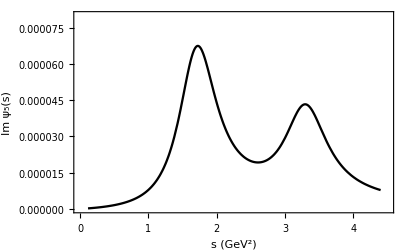
```mathematica
(*-Graphics-;*)
```

```mathematica
(*Calculating Subscript[m, ud](s)*)
mudCIPTbeyondchiral=CIPTmassFESR[s0,aint0,sint0,modelBPdR2[s,1,260,208,0.1],kern1,GluonCon,1,d2phi5][[1]]
mudErrorCIPTbeyondchiral =MassErrorFESR[s0,modelBPdR2[s,1,260,208,0.1],kern1,CIPTmassFESR,d2phi5]
```

4.28924
{{4.28924, "Mass MeV"}, {-0.224555, "Δα"}, {-0.056639, "ΔGG"}, {0.0316488, "Δs0"}, {4.27572, 4.33902, "Min s0 and Max s0"}, {0.103582, "Model Error"}, {-0.143301, "Unknown 6-loop PQCD term"}, {0.293085, "Total"}}

We note that the quark mass m_ud(s) obtained by modelling the full hadronic spectral function beyond the chiral limit, is comparable to the quark mass obtained by modelling the hadronic spectral function in the chiral limit; and that the shape of the hadronic model is the same. However, modelling the spectral function in the chiral limit is an approximation, and should not be used in the final quark mass determinations.

## Taylor expanding √δPQCD series

Here, we Taylor expand the √δPQCD series in order to improve the convergence of this series.  The expressions for the series, before and after the Taylor expansion, can be found in our paper: Dominguez , Mes, Schilcher, ‘Up- and Down- Quark Masses from QCD Sum Rules’, (2018). Here examine numerical effect of performing the Taylor expansion on the quark mass m_ud(s) and the region of stability. 
Note: This is done through using Fixed Order Perturbation Theory, since α_s is frozen around the circular contour; and this allows for series expansions in terms of α_s.

```mathematica
Clear[expand];
expand=-1/2;
```

```mathematica
(*Calculating Subscript[m, ud](s)*)
```

```mathematica
mudFOPTt=FOPTmassFESR[s0,aint0,sint0,modelBPdR[s,1,260,208,0.1],kern1,GluonCon,1,phi5A][[1]]
mudErrorFOPTt=MassErrorFESR[s0,modelBPdR[s,1,260,208,0.1],kern1,FOPTmassFESR,phi5A]
```

3.14907
{{3.14907, "Mass MeV"}, {-0.42928, "Δα"}, {0.00001, "ΔGG"}, {0.06373, "Δs0"}, {3.03233, 3.15980, "Min s0 and Max s0"}, {0.08103, "Model Error"}, {0.24408, "Unknown 6-loop PQCD term"}, {0.50447, "Total"}}

```mathematica
(*Note: the uncertainty due to the unknown higher order terms in the δPQCD series above, must be calculated manually*)
```

```mathematica
(*Graphically viewing the stability of the quark masses after taylor expanding the √δPQCD series*)
fopttaylordata=Table[{i,FOPTmassFESR[i,aint0,sint0,modelBPdR[s,1,260,208,0.1],kern1,GluonCon,1,phi5A][[1]]},{i,1,4.0,0.1}]
```

{{1., 2.30612}, {1.1, 2.4164}, {1.2, 2.51657}, {1.3, 2.60513}, {1.4, 2.68249}, {1.5, 2.75022}, {1.6, 2.81037}, {1.7, 2.86473}, {1.8, 2.91416}, {1.9, 2.95864}, {2., 2.99783}, {2.1, 3.03167}, {2.2, 3.06041}, {2.3, 3.08449}, {2.4, 3.10442}, {2.5, 3.12073}, {2.6, 3.13385}, {2.7, 3.14414}, {2.8, 3.15186}, {2.9, 3.1571}, {3., 3.1598}, {3.1, 3.15971}, {3.2, 3.15633}, {3.3, 3.14907}, {3.4, 3.1373}, {3.5, 3.1205}, {3.6, 3.0981}, {3.7, 3.06921}, {3.8, 3.03233}, {3.9, 2.9851}, {4., 2.92383}}

```mathematica
foptplot2=ListLinePlot[{fopttaylordata},Frame-> True,FrameStyle->Thick,FrameLabel-> {"s_0 (GeV^2)","m_ud(2 GeV) (MeV)"},PlotStyle-> {Directive[Thickness[0.004],Black], Directive[Thickness[0.004],Black]},PlotRange-> {{1.45,4.05},{1,4}}, PlotLabel->"Fixed Order Perturbation Theory with taylor expansion of√δPQCD series"]
```

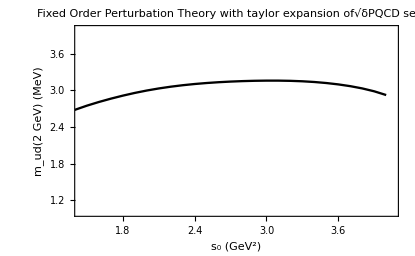
```mathematica
(*-Graphics-;*)
```

The quark mass m_ud(s), is calculated using the Taylor expansion and is now much smaller than our previous determinations using FOPT or CIPT. The behaviour of m_ud(s) over a range of s values has also changed, and the stability window is not as pronounced. Since, the FOPT and CIPT determinations are in close agreement with each other and there is no further evidence leading us to suspect that the Taylor expansion method is correct (besides the improved convergence of the series); we decide to not favour this method as the final determination. It must, however, be remarked that using this method of Taylor expanding the  √δPQCD series results in  values for the light quark mass m_ud(s), which are in close agreement with Lattice QCD.